```mathematica
h=6.626*^-34;
ℏ=h/(2π);
μ0=4π*1*^-7;
γY=2.1*^6;
IY=0.5;
IV=7/2;
γV=11.2*^6;
kB=1.38*^-23;
μB=9.27*^-24;
γYb=(6*μB)/h;
```

```mathematica
Sech[((6*μB*0.06)/(2*kB*0.7))]^2
Sech[((6*μB*0.44)/(2*kB*0.7))]^2
```

0.970747

0.272557

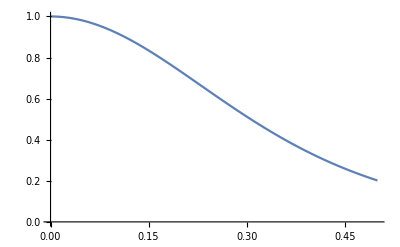

```mathematica
Plot[Sech[((6*μB*B)/(2*kB*0.7))]^2,{B,0,0.5},AxesOrigin->{0,0}]
```

```mathematica
tt440={0.4005,0.4796,0.5851,0.6852,0.7801,0.8961,0.991,1.0966,1.1914,1.2968,1.397,1.5024,1.6237,1.6974,1.8082,1.9189,1.9768,2.2403,2.5144,2.7306,3.0099,3.2417,3.5053,3.7582,4.0165,4.2589,4.5224,4.7753,5.0177,5.2495,5.4812,5.7393,6.0029,6.2609,6.5083,6.756,6.998,7.2563,7.4983,7.7614,8.0145,8.5088,8.7516}/1000;
ee440={0.8199,0.7894,0.7931,0.76,0.7457,0.7562,0.7212,0.7279,0.6814,0.6654,0.6258,0.6227,0.5856,0.5481,0.548,0.5276,0.5057,0.4493,0.4049,0.3718,0.3367,0.284,0.2488,0.2201,0.1955,0.1681,0.1438,0.1248,0.1063,0.0893,0.0715,0.0576,0.0516,0.0404,0.0296,0.0262,0.0175,0.0157,0.0101,7.39*^-3,6.63*^-3,2.61*^-3,2.92*^-3};
data440=Transpose[{tt440,ee440}];
dataLogSq440=Transpose[{tt440,Log[ee440^2]}];
tt60={0.2028,0.2084,0.2403,0.2748,0.2883,0.3306,0.3465,0.3576,0.3921,0.4134,0.4612,0.4909,0.5199,0.5438,0.5705,0.5949,0.6158,0.6526,0.6768}/1000;
ee60={0.8998,0.7109,0.5819,0.4686,0.3826,0.3409,0.3059,0.2128,0.1682,0.1502,0.1127,0.0705,0.0662,0.0566,0.0451,0.0287,0.0306,0.032,0.0222};
data60=Transpose[{tt60,ee60}];
dataLogSq60=Transpose[{tt60,Log[ee60^2]}];
```

{I0→-0.38242,Γ0→0.0156353,ΓSDR→0.0203442}

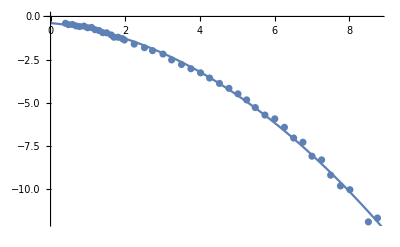

{I0→-0.516515,Tm→6.83448,x→1.8469}

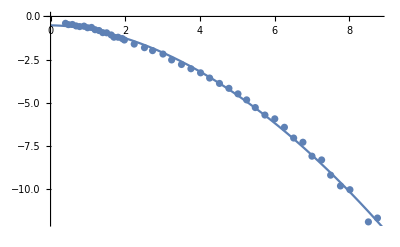

```mathematica
sol=FindFit[dataLogSq440,I0-4*t*π*(Γ0+1/2 ΓSDR*t),{I0,Γ0,ΓSDR},t]
Show[ListPlot[dataLogSq440], Plot[I0-4*t*π*(Γ0+1/2 ΓSDR*t)/.sol,{t,0,10.7}]]
sol=FindFit[dataLogSq440,I0-2*((2t)/Tm)^x,{I0,Tm,x},t]
Show[ListPlot[dataLogSq440], Plot[I0-2*((2t)/Tm)^x/.sol,{t,0,10.7}]]
```

{I0→2.68794,Γ0→1.23602,ΓSDR→0.0000517624}

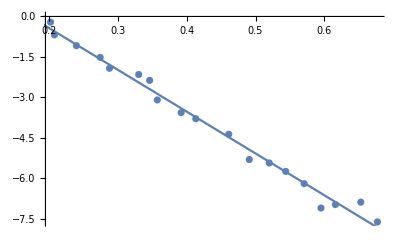

{I0→4.03875,Tm→0.155834,x→0.819204}

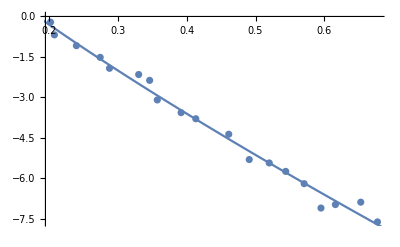

```mathematica
sol=FindFit[dataLogSq60,{I0-4*t*π*(Γ0+1/2 ΓSDR*t),{ΓSDR>0}},{I0,Γ0,ΓSDR},t]
Show[ListPlot[dataLogSq60], Plot[I0-4*t*π*(Γ0+1/2 ΓSDR*t)/.sol,{t,0,0.7}]]
sol=FindFit[dataLogSq60,{I0-2*((2t)/Tm)^x,{Tm>0}},{I0,Tm,x},t]
Show[ListPlot[dataLogSq60], Plot[I0-2*((2t)/Tm)^x/.sol,{t,0,0.7}]]
```

```mathematica
neY=(33791/2)/(4/3*π*(Sqrt[56.95^2+56.95^2+50.31^2]*10^-10)^3)(*Num density of Y*)
```

4.71019×10^27

```mathematica
CubeRoot[1/(neY*100*^-6)]/10^-10
```

128.525

```mathematica
Sqrt[17.80^2+14.24^2+14.15^2]
```

26.8298

```mathematica
(26.8/128.5)^-3
```

110.231

```mathematica
(h*γY*IY*0.1)/(kB*0.7)
Sech[%](*Nuclear magnetic flip suppression factor*)
(h*γV*IV*0.1)/(kB*0.7)
Sech[%](*Nuclear magnetic flip suppression factor*)
```

7.20217×10^-6

1.

0.000268881

1.

```mathematica
(*Equation 15 in Bottger*)
Ryy=0.25*μ0*h*γY^2*4.7*^27*Sqrt[1/2*3/2](*Expected Y flip rate*)
1000/Ryy(*Y flip time in ms*)
Rvv=0.25*μ0*h*γV^2*4.7*^27*Sqrt[7/2*9/2](*Expected V flip rate*)
1000/Rvv(*V flip time in ms*)
(*Compare to the spin coherence time of 3.5ms from Arcangeli et al paper in Eu:YSO*)
```

3.73653

267.628

487.052

2.05317

```mathematica
0.14*μ0*γY*0.001*μB*neY*Sqrt[1/2*3/2]
0.14*μ0*γV*0.001*μB*neY*Sqrt[7/2*9/2]
0.14*μ0*γY*neY*Sqrt[1/2*3/2]*2*h*10^4
0.14*μ0*γV*neY*Sqrt[7/2*9/2]*2*h*10^4
(*Equation 13 in Bottger, removed the |g_g-g_e|*μB*Spin term and converted from Hz to Hz/T.J to T to G. This gives the expected spread in B field caused by the flipping Y and V atoms ignoring flip rate. We compare this to the magnitude of the FWHM sigmas that we got for neighs 235-1000. We have 2.288e-5T for V only and 9.51e-7T for Y only. If we use neighbours from 0-100,we have 2.5e-6T for Y only and 3.72e-4T for V only. *)
```

13.9703

341.44

0.0199714

0.488108

```mathematica
π/(9Sqrt[3])*(μ0*0.001*6*μB^2*neY*100/10^6)/h
π/(9Sqrt[3])*(μ0*6*μB*neY*100/10^6)/h*2*h*10^4(*Equation 8 from Bottger, gives the expected spread in B field due to flipping neighbour Yb REIs. The density is taken to be 100ppm. Similar to above, converted from their Gamma(Hz) spread in energy level to a spread in B field by dividing by the |g_g-g_e|*μB*Spin then convert to Gauss*)
```

92.8228

0.132696

```mathematica
92.8228*15000*0.27(*Calculating ΓSD*R*sech^2 assuming R is 15kHz. The sech^2 factor was computed above.*)
```

375932.

{I0→2.67005,Γ0→1228.6}

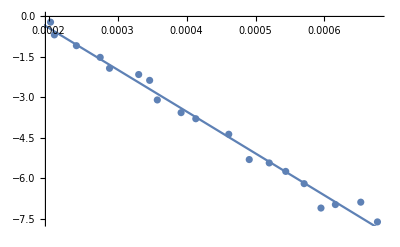

```mathematica
sol=FindFit[dataLogSq60,{I0-4*t*π*(Γ0+1/2(0.049*0.001*μB*1/2)/(10000*h)*1000/2*t),{Γ0>0}},{I0,Γ0},t]
Show[ListPlot[dataLogSq60], Plot[I0-4*t*π*(Γ0+1/2(0.049*0.001*μB*1/2)/(10000*h)*1000/2*t)/.sol,{t,0,0.01}]]
```

```mathematica
Sqrt[1/(15*^-6)*2π*150*^6]*(4π*ℏ)/(2.53*μB*7*^23)
```

6.39842×10^-28

```mathematica
1/(270*^-6*π)//N
```

1178.93